```mathematica
QS=Import["~/share/gpu-sampler/QS.csv"];
```

```mathematica
QS//Dimensions
```

{46080,2}

```mathematica
Covariance[QS]
```

{{1.10888,1.10888},{1.10888,1.10888}}

```mathematica
QS//Dimensions
```

{46080,2}

{1.07262,1.06918}

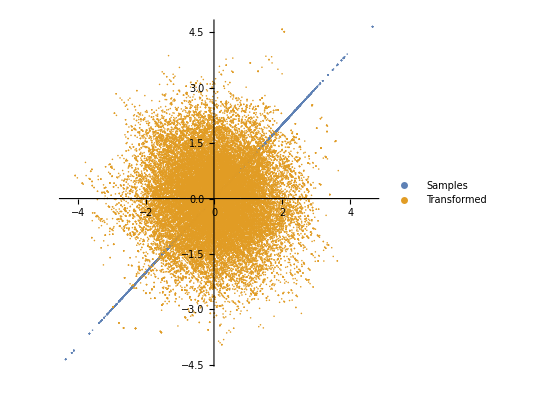

```mathematica
ρ=1-1/10^7;
SIGMA={{1,ρ},{ρ,1}};
 QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[{QS,QS1},PlotStyle->Opacity[1],AspectRatio->1,PlotLegends->{Samples, Transformed}]
```